```mathematica
D[1/(-2*a*u^3+b*Sqrt[1-u^4]),u]
```

```mathematica
h[a_,b_,u_]:=Abs[-(-6 a u^2-(2 b u^3)/(√(1-u^4)))/((-2 a u^3+b √(1-u^4))^2)]
```

```mathematica
D[Sqrt[1-u^4],u]
```

-(2 u^3)/(√(1-u^4))

```mathematica
D[-(1-u^2)^(1/4),u]
```

u/(2 (1-u^2)^(3/4))

```mathematica
Det[{{(Sqrt[1-u^4])/2, -2u^3/Sqrt[1-u^4]},{(1/4)*u , 1  } }]//Simplify
```

1/(2 √(1-u^4))

```mathematica
D[-(1-u^2)^(1/4),u]
```

u/(2 (1-u^2)^(3/4))

```mathematica
Det[{{  (1/2)*u  ,   1}, {  -(1-u^2)^(1/4)/4  ,u/(2 (1-u^2)^(3/4)) }}]//Simplify
```

1/(4 (1-u^2)^(3/4))

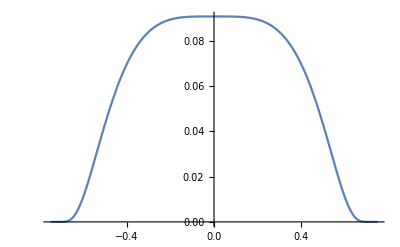

```mathematica
Plot[Exp[1/(Sqrt[1-u^4]^2+0.75^4)]*Exp[1/(u^4-0.75^4)],{u,-0.75,0.75}]
```

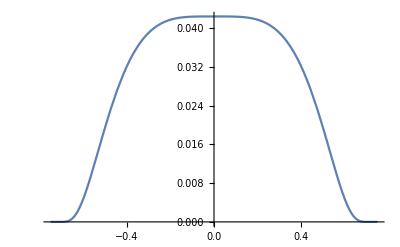

```mathematica
Plot[Exp[1/(u^4-0.75^4)],{u,-0.75,0.75}]
```

```mathematica
D[Exp[1/(x^4-1)],x]//Simplify
```

-(4 ⅇ^(1/(-1+x^4)) x^3)/((-1+x^4)^2)

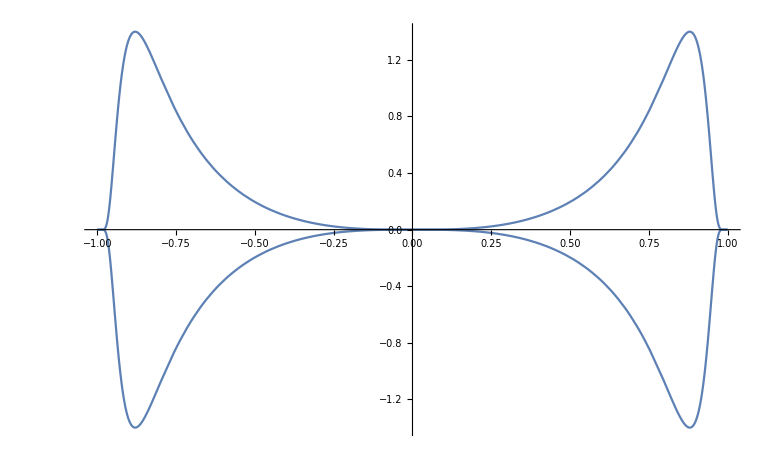

```mathematica
Show[Plot[-(4 ⅇ^(1/(-1+x^4)) x^3)/((-1+x^4)^2),{x,-1,1}],Plot[(4 ⅇ^(1/(-1+x^4)) x^3)/((-1+x^4)^2),{x,-1,1}]]
```

```mathematica
-(4 ⅇ^(1/(-1+x^4)) x^3)/((-1+x^4)^2)-(4 ⅇ^(1/(-1+x^4)) x^3)/((-1+x^4)^2)
```

```mathematica
1/(x^2-1) + 1/(y^4-1)//Simplify
```

1/(-1+x^2)+1/(-1+y^4)

```mathematica
Plot3D[Exp[1/(x^2+y^4-1)],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

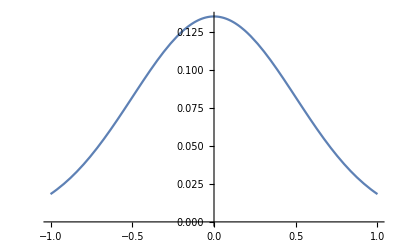

```mathematica
Plot[E^(-(x-1)^2)*E^(-(x+1)^2),{x,-1,1}]
```

```mathematica
Integrate[E^(-(x-1)^2)*E^(-(x+1)^2),{x,0,A}]
```

(√(π/2) Erf[√2 A])/(2 ⅇ^2)

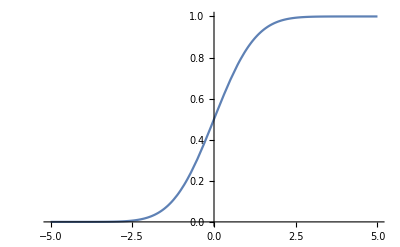

```mathematica
Plot[(1/2)(1+ Erf[u/Sqrt[2]]),{u,-5,5}]
```

```mathematica
D[Sqrt[1-u^4],u]
```

-(2 u^3)/(√(1-u^4))

```mathematica
D[Sqrt[1-u^4],{u,1}]//FullSimplify
```

-(2 u^3)/(√(1-u^4))

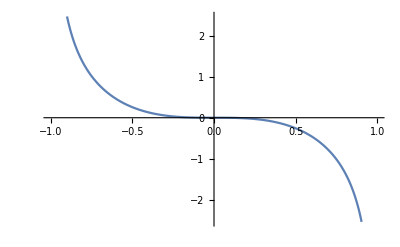

```mathematica
Plot[-(2 u^3)/(√(1-u^4)),{u,-1,1}]
```

```mathematica
D[Sqrt[1-u^4],{u,2}]//FullSimplify
```

(2 u^2 (-3+u^4))/((1-u^4)^(3/2))

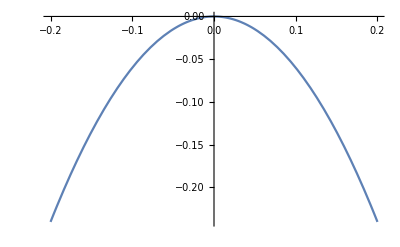

```mathematica
Plot[(2 u^2 (-3+u^4))/((1-u^4)^(3/2)),{u,-0.2,0.2}]
```

```mathematica
D[Sqrt[1-u^4],{u,4}]//FullSimplify
```

-(12 (1+14 u^4+5 u^8))/((1-u^4)^(7/2))

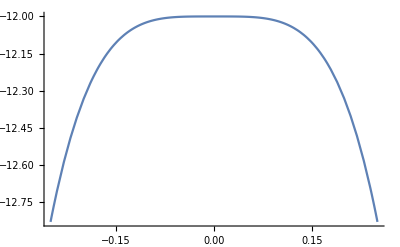

```mathematica
Show[Plot[-(12 (1+14 u^4+5 u^8))/((1-u^4)^(7/2)),{u,-0.25,0.25}],Plot[0,{u,-0.5,0.5}]]
```

```mathematica
D[Sqrt[1-u^4],{u,5}]//FullSimplify
```

-(120 u^3 (7+3 u^4 (6+u^4)))/((1-u^4)^(9/2))

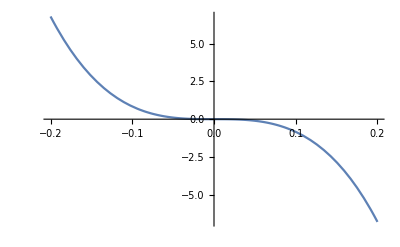

```mathematica
Plot[-(120 u^3 (7+3 u^4 (6+u^4)))/((1-u^4)^(9/2)),{u,-0.2,0.2}]
```

```mathematica
D[Sqrt[1-u^4],{u,8}]//FullSimplify
```

-(5040 (1+240 u^4+2190 u^8+3380 u^12+1017 u^16+36 u^20))/((1-u^4)^(15/2))

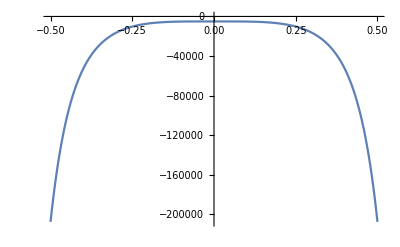

```mathematica
Plot[-(5040 (1+240 u^4+2190 u^8+3380 u^12+1017 u^16+36 u^20))/((1-u^4)^(15/2)),{u,-0.5,0.5}]
```

```mathematica
D[(1-u^2)^(1/4),{u,1}]//FullSimplify
```

-u/(2 (1-u^2)^(3/4))

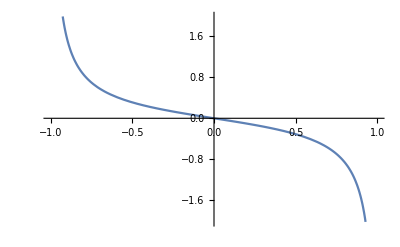

```mathematica
Plot[-u/(2 (1-u^2)^(3/4)),{u,-1,1}]
```

```mathematica
D[(1-u^2)^(1/4),{u,2}]//FullSimplify
```

-(2+u^2)/(4 (1-u^2)^(7/4))

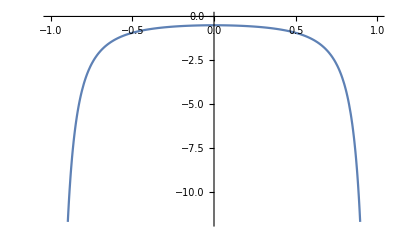

```mathematica
Plot[-(2+u^2)/(4 (1-u^2)^(7/4)),{u,-1,1}]
```

```mathematica
Integrate[E^(-I*λ*x^2)*x^L*E^(-x^2),{x,-A,A}]
```

1/2 (1+ⅈ λ)^(1/2 (-1-L)) (-A ((-A)^L+A^L) (1+ⅈ λ)^((1+L)/2) ExpIntegralE[(1-L)/2,A^2 (1+ⅈ λ)]+(1+(-1)^L) Gamma[(1+L)/2,0])

```mathematica
Integrate[1/x^(2N-L),{x,2,Infinity}]
```

ConditionalExpression[-2^(1+L-2 N)/(1+L-2 N),Re[L-2 N]<-1]

```mathematica
Integrate[Abs[x]^(k+1),{x,-A,A}]
```

ConditionalExpression[(2 A^(2+k))/(2+k),Re[k]>-2&&Re[A]≥0&&Im[A]==0]

```mathematica
f[α_]:=2(k-1)*( 2/(λ*α) + (α/δ)^(1/(k-1)) )
```

```mathematica
f[δ^(1/k)*(2(k-1)/λ)^(1/(k-1))]//Simplify
```

2 (-1+k) ((2^(1/(-1+k)) δ^(-1+1/k) ((-1+k)/λ)^(1/(-1+k)))^(1/(-1+k))+(2^((-2+k)/(-1+k)) δ^(-1/k) ((-1+k)/λ)^(1/(1-k)))/λ)

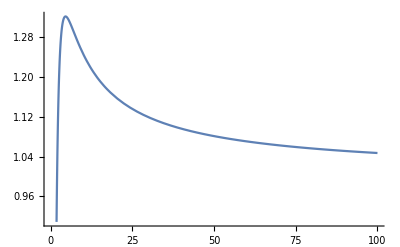

```mathematica
Plot[(k-1)^(1/k),{k,0,100}]
```

```mathematica
D[f[α],α]//Simplify
```

(2 (2-2 k+α (α/δ)^(1/(-1+k)) λ))/(α^2 λ)

```mathematica
f[α]
```

2 (-1+k) ((α/δ)^(1/(-1+k))+2/(α λ))

```mathematica
D[f[α],{α,1}]
```

2 (-1+k) ((α/δ)^(-1+1/(-1+k))/((-1+k) δ)-2/(α^2 λ))

```mathematica
D[f[α],{α,2}]
```

2 (-1+k) (((-1+1/(-1+k)) (α/δ)^(-2+1/(-1+k)))/((-1+k) δ^2)+4/(α^3 λ))

```mathematica
D[f[α],{α,2}] // FullSimplify//TeXForm
```

\frac{2 (k-1)
   \left(\frac{4}{\lambda
   }-\frac{\alpha  (k-2)
   \left(\frac{\alpha }{\delta
   }\right)^{\frac{1}{k-1}}}{(
   k-1)^2}\right)}{\alpha ^3}

```mathematica
fpp[α_]:=(2 (-1+k) (-((-2+k) α (α/δ)^(1/(-1+k)))/(-1+k)^2+4/λ))/α^3;
```

```mathematica
fpp[(δ)^(1/k)*(2(k-1)/λ)^(1-1/k)]//Simplify
```

2^(-2+3/k) δ^(-3/k) (-((-2+k) δ (2^((-1+k)/k) δ^(-1+1/k) ((-1+k)/λ)^((-1+k)/k))^(k/(-1+k)))/(-1+k)^2+4/λ) ((-1+k)/λ)^(-2+3/k) λ

```mathematica
f[α_]:=4*k/(λ*α) + 2(k-1)(α/δ)^(1/(k-1))
```

```mathematica
f[(δ^(1/k))*(2k/λ)^(1-1/k)]//Simplify
```

2 δ^(-1/k) ((-1+k) δ^(1/k) (2^((-1+k)/k) δ^(-1+1/k) (k/λ)^((-1+k)/k))^(1/(-1+k))+2^(1/k) (k/λ)^(1/k))

```mathematica
D[4*k/(λ*α) + 2(k-1)(α/δ)^(1/(k-1)),α]//Simplify
```

(2 (-2 k+α (α/δ)^(1/(-1+k)) λ))/(α^2 λ)

```mathematica
D[4*k/(λ*α) + 2(k-1)(α/δ)^(1/(k-1)),{α,2}]//Simplify
```

(2 ((-1+1/(-1+k)) α (α/δ)^(1/(-1+k))+(4 k)/λ))/α^3

```mathematica
fpp[α_]:=(2 ((-1+1/(-1+k)) α (α/δ)^(1/(-1+k))+(4 k)/λ))/α^3;
```

```mathematica
fpp[(δ^(1/k))*(2k/λ)^(1-1/k)]//Simplify
```

2^(-2+3/k) δ^(-3/k) ((-1+1/(-1+k)) δ (2^((-1+k)/k) δ^(-1+1/k) (k/λ)^((-1+k)/k))^(k/(-1+k))+(4 k)/λ) (k/λ)^(-3+3/k)

```mathematica
Solve[-2 k+α (α/δ)^(1/(-1+k)) λ==0,α]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-2 k+α (α/δ)^(1/(-1+k)) λ==0,α]

```mathematica
2^(-1/(-2+2/(1-k)-k/(1-k))) (λ/k)^(1/(-2+2/(1-k)-k/(1-k)))//Simplify
```

2^((-1+k)/k) (λ/k)^(-1+1/k)

```mathematica
f[α_]:= 4*k/(λ*α) + 2(k-1)α^(1/(k-1));
```

```mathematica
f[2^((-1+k)/k) (λ/k)^(-1+1/k)]//FullSimplify
```

2 (2^(1/k) (λ/k)^(-1/k)+(-1+k) (2^((-1+k)/k) (λ/k)^(-1+1/k))^(1/(-1+k)))

```mathematica
(-1+1/k)*(1/(-1+k))//Simplify
```

-1/k

```mathematica
D[4*k/(λ*α) + 2(k-1)α^(1/(k-1)),{α,2}]//Simplify
```

2 (-1+1/(-1+k)) α^(-2+1/(-1+k))+(8 k)/(α^3 λ)

```mathematica
fpp[α_]:=2 (-1+1/(-1+k)) α^(-2+1/(-1+k))+(8 k)/(α^3 λ);
```

```mathematica
fpp[2^((-1+k)/k) (λ/k)^(-1+1/k)]//Simplify
```

(8^(1/k) λ^2 (λ/k)^(-3/k))/k^2+2 (-1+1/(-1+k)) (2^((-1+k)/k) (λ/k)^(-1+1/k))^(-2+1/(-1+k))

```mathematica
2 (-1+1/(-1+k)) (2^((-1+k)/k) (λ/k)^(-1+1/k))^(-2+1/(-1+k))+(8 k)/((2^((-1+k)/k) (λ/k)^(-1+1/k))^3 λ)//FullSimplify
```

(8^(1/k) λ^2 (λ/k)^(-3/k))/k^2+2 (-1+1/(-1+k)) (2^((-1+k)/k) (λ/k)^(-1+1/k))^(-2+1/(-1+k))

```mathematica
(a+b)^3//Expand
```

a^3+3 a^2 b+3 a b^2+b^3